# Mutualism Parasitism Balance

```mathematica
Clear["Global`*"]
```

### Model and Pars

```mathematica
tmax=8; (* 8-week time set *)
parsFixed={nhn->0.18,nsn->0.13}; (*fixed parameters*)
sim[pars_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f},(*Simulation*)
f=s[t](a h[t])/(s[t]+a w h[t]);(*equation 13*)
jsc=p s[t]; (*equation 6*)
jsn=yn nhn f; (*equation 5*)
jhc= p s[t]-Min[jsc,nsn^-1 jsn]+rc h[t]^(2/3);(*equations 10 and 11*)
jhn=rn  h[t]^(2/3);(*equation 9*)
jsg=Min[jsc,nsn^-1 jsn]; (*equation 3*)
jst=ds s[t]; (*equation 4*)
jhg=Min[jhc,nhn^-1 jhn];(*equation 7*)
jht=dh h[t] + f;(*equation 8*)
Quiet@NDSolve[
{
s'[t]==jsg-jst,(*equation 1*)
h'[t]==jhg-jht,(*equation 2*)
s[0]==s0,
h[0]==h0
}/.pars,
{s,h},
{t,0,tmax},Method->{Automatic,"DiscontinuityProcessing"->None},WorkingPrecision->20][[1]]];
pars[treatment_]:=(*parameter choices function*)Piecewise[{{Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->0,h0->h0X},parsFixed], treatment=="as"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->0,h0->h0X},parsFixed], treatment=="af"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->s0X,h0->h0X},parsFixed], treatment=="if"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->s0X,h0->h0X},parsFixed], treatment=="is"}}]
bestfit={aX->0.07243165880437435,wX->0.0026142991079086157,pX->27.700459925037663,ynX->0.060192963245436854,dsX->0.7709975010970849,dhX->0.12619563820188512,h0X->6.502940605096842*^-6,s0X->1.0227841615913929*^-10,rcX->0.009992087726261166,rnX->0.014645292219590888};(*best fit parameter values*)
```

### δ Comparison Plots

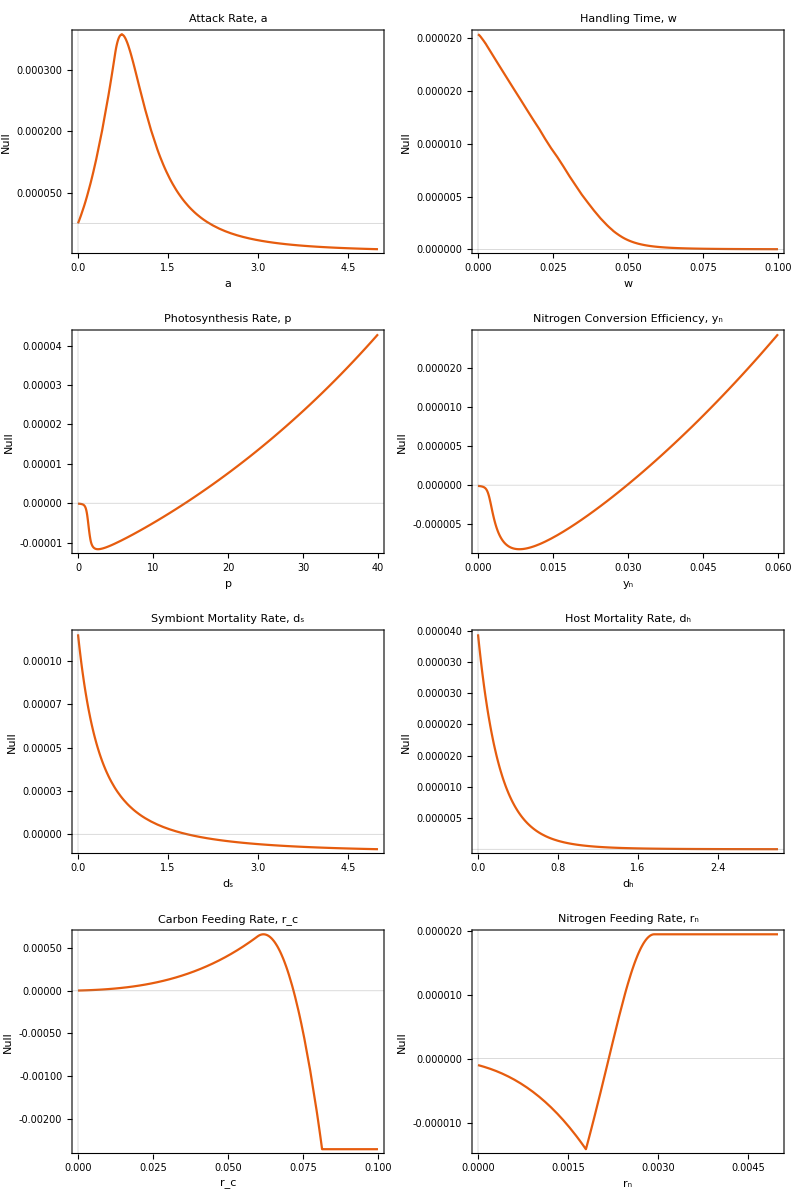
-Graphics-Magnitude of Parasitisn or Mutualism, δ

/Users/JakobK-R/Dropbox/Peng_Anemone/Paper_Post_Revision/deltplot.jpg

```mathematica
myticks= Function[{number},{number,ToString[AccountingForm[N[number],{1,sf},NumberSigns->{"-",""},NumberPadding->{" ","0"}]]}];
tk[sfn_]:=myticks/.sf->sfn(*plot tick functions*)

mutploter[var_,xrange_,yrange_,ynum_,sf_,label_,xlab_]:= (*δ plot function*)Plot[Evaluate[h[8]/.sim[pars["if"]/.var->x/.bestfit]]-Evaluate[h[8]/.sim[pars["af"]/.var->x/.bestfit]],xrange,PlotLabel->Style[label,FontSize->15],LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},FrameTicks->{{tk[sf]/@FindDivisions[yrange,ynum],None},{Automatic,None}},
PlotTheme->"Scientific",AxesLabel->{Style[xlab,FontFamily->"Times New Roman",FontColor->Black,FontSize->15],Null},WorkingPrecision->100,ImageSize->400,PlotRange->All]
aplot=Quiet[mutploter[aX,{x,0,5},{-0.00005,0.0003},7,6,"Attack Rate, a","a"]] ;(*attack rate*)
wplot=Plot[Evaluate[h[8]/.sim[pars["if"]/.wX->x/.bestfit]]-Evaluate[h[8]/.sim[pars["af"]/.wX->x/.bestfit]],{x,0,0.1},PlotLabel->Style["Handling Time, w",FontSize->15],LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},AxesLabel->{Style["w",FontFamily->"Times New Roman",FontColor->Black,FontSize->15],Null},WorkingPrecision->100,ImageSize->400,PlotRange->All,FrameTicks->{{tk[6]/@FindDivisions[{0,2 10^-5},5],None},{
Automatic,None}},
PlotTheme->"Scientific",AxesStyle->{Black,Thick}];(*handeling time*)
pplot=Quiet[mutploter[pX,{x,0,40},{-0.00001,0.00004},6,5,"Photosynthesis Rate, p","p"]];(*Photosynthesis rate*)
ynplot=Quiet[mutploter[ynX,{x,0,.06},{-0.00001,0.00002},6,6,"Nitrogen Conversion Efficiency,"Subscript["y","n"],Subscript["y","n"]]];(*nitrogen conversion efficiency*)
dsplot=Quiet[mutploter[dsX,{x,0,5},{0,0.00012},5,5,"Symbiont Mortality Rate,"Subscript["d","s"],Subscript["d","s"]]];(*symbiont mortality*)
dhplot= Quiet[mutploter[dhX,{x,0,3},{0.000005,0.000035},6,6,"Host Mortality Rate,"Subscript["d","h"],Subscript["d","h"]]];(*host mortality*)
rcplot=Quiet[mutploter[rcX,{x,0,0.1},{-0.0015,0.0005},5,5,"Carbon Feeding Rate,"Subscript["r","c"],Subscript["r","c"]]];(*host carbon uptake rate*)
rnplot=Quiet[mutploter[rnX,{x,0,0.005},{-0.000015,0.00003},7,6,"Nitrogen Feeding Rate,"Subscript["r","n"],Subscript["r","n"]]];(*host nitrogen uptake rate*)
deltacom=Labeled[Grid[{
{aplot,wplot},
{pplot,ynplot},
{dsplot,dhplot},
{rcplot,rnplot}
}],Style["Magnitude of Parasitisn or Mutualism, δ",FontFamily->"Times New Roman",FontColor->Black,FontSize->25],{Left},RotateLabel->True](*Figure 4*)
Export[NotebookDirectory[]<>"deltplot.jpg",deltacom]
```

### Heat Plots

```mathematica
γ=bestfit[[10,2]]/bestfit[[9,2]]; (*calculate γ*)

f[r_,p_]:=Quiet[(h[8]/.sim[pars["if"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit])-(h[8]/.sim[pars["af"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit])](*define δ function for varrying R and p*)
f2[r_?NumericQ,p_?NumericQ]:=Quiet[(h[8]/.sim[pars["if"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit])-(h[8]/.sim[pars["af"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit])](*set up to minimize r*)
f3[r_?NumericQ,p_?NumericQ]:=Quiet[(h[8]/.sim[pars["if"]/.pX->p/.{rcX->r,rnX->γ r}/.bestfit])-(h[8]/.sim[pars["af"]/.pX->p/.{rcX->r,rnX->γ r}/.bestfit])]
(*set up to minimize p*)
turnup=
{x/.NMinimize[{Abs[f2[x,11.11]],0.00014<x<0.0007},{x}][[2]],11.11};(*calculate important turning point of δ=0 line*)
curve3=Table[{r,p/.NMinimize[{Abs[f3[r,p]],10<p<15},{p}][[2]]},{r,0.0001,0.0007,0.0001}];
(*calculate early part of horizontal curve for δ=0*)
vert=ParallelTable[
{x/.NMinimize[{Abs[f2[x,p]],0<x<0.0005},{x}][[2]],p},{p,0,30,1}];
(*calculate verticle curve for δ=0*)
curve=ParallelTable[
{x/.NMinimize[{Abs[f2[x,p]],0.0005<x},{x}][[2]],p},{p,11,13,.25}];
(*calculate horizontal curve for δ=0*)
full=SortBy[Join[curve3[[2;;7]],vert[[13;;31]],curve,{turnup}],First];(*δ=0 points*)
```

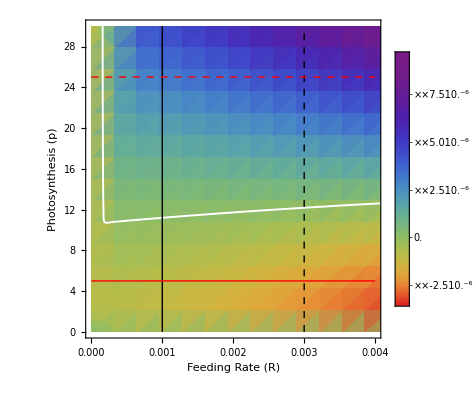
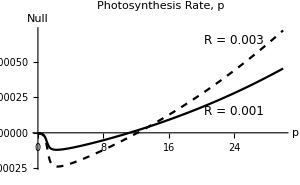
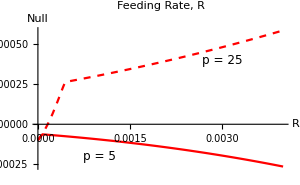
-Graphics-A | 
-Graphics-δB | -Graphics-δC

/Users/JakobK-R/Dropbox/Peng_Anemone/Paper_Post_Revision/heatplot.jpg

```mathematica
heatplot=Quiet[Show[DensityPlot[f[r,p],{r,0,0.0045},{p,0,30},FrameLabel->{Style["Feeding Rate (R)",FontFamily->"Times New Roman",FontColor->Black,FontSize->15],Style["Photosynthesis (p)",FontFamily->"Times New Roman",FontColor->Black,FontSize->15]},ColorFunction->(ColorData["Rainbow",(1-#)^2]&),LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->10},
PlotRange->{{0,0.004},{0,30}},PlotLegends->BarLegend[Automatic,LegendLabel->Style["δ   ",FontFamily->"Times New Roman",FontColor->Black,FontSize-> 20],"StyledContours"->Transpose[{ticks,{x,White,x,x,x}/.x->Opacity[0]}],Ticks->ticks],ImageSize->400,WorkingPrecision->100],
ListPlot[full,Joined->True,PlotStyle->{White,Thickness[.0035]},InterpolationOrder->2],
Graphics[{Thick,Black,Line[{{0.001,0},{0.001,30}}]}],
Graphics[{Thick,Black,Dashed,Line[{{0.003,0},{0.003,30}}]}],
Graphics[{Thick,Red,Line[{{0,5},{0.004,5}}]}],
Graphics[{Thick,Red,Dashed,Line[{{0,25},{0.004,25}}]}]
]]; (*Figure 5A*)
aextra=Quiet[
Labeled[
Plot[{f[0.001,x],f[0.003,x]},{x,0,30},PlotLabel->Style["Photosynthesis Rate, p",FontSize->15],PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},AxesOrigin->{0,0},AxesLabel->{Style["p",FontFamily->"Times New Roman",FontColor->Black,FontSize->15],Null},WorkingPrecision->40,ImageSize->300,
PlotStyle->{{Thick, Black},{Thick, Black,Dashed}},
Epilog->{
Text[Style["R = 0.001",FontFamily->"Times New Roman",FontColor->Black,FontSize->12],{24,1.5 10^-6}],Text[Style["R = 0.003",FontFamily->"Times New Roman",FontColor->Black,FontSize->12],{24,6.5 10^-6}]}],
Style["δ",FontFamily->"Times New Roman",FontSize->15],{Left}]];(*Figure 5B*)
Rextra=Quiet[Labeled[Plot[{f[x,5],f[x,25]},{x,0,0.004},PlotLabel->Style["Feeding Rate, R",FontSize->15],PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},AxesOrigin->{0,0},AxesLabel->{Style["R",FontFamily->"Times New Roman",FontColor->Black,FontSize->15],Null},WorkingPrecision->40,ImageSize->300,PlotStyle->{{Thick, Red},{Thick, Red,Dashed}},
Epilog->{
Text[Style["p = 5",FontFamily->"Times New Roman",FontColor->Black,FontSize->12],{0.001,-2 10^-6}],Text[Style["p = 25",FontFamily->"Times New Roman",FontColor->Black,FontSize->12],{0.003,4 *10^-6}]}],Style["δ",FontFamily->"Times New Roman",FontSize->15],{Left}]];(*Figure 5C*)
fullheatplot=Grid[{
{Panel[heatplot,Style["A",Bold,FontFamily->"Times New Roman",FontSize->25],{{Left,Top}},Background->White,Appearance->Frame,ImageMargins->10],SpanFromLeft},
{Panel[aextra,Style["B",Bold,FontFamily->"Times New Roman",FontSize->25],{{Left,Top}},Appearance->Frame,Background->White],Panel[Rextra,Style["C",Bold,FontFamily->"Times New Roman",FontSize->25],{{Left,Top}},Appearance->Frame,Background->White]}}]
Export[NotebookDirectory[]<>"heatplot.jpg",fullheatplot] (*Full Figure 5*)
```